# CRNSSA Runtime Testing

```mathematica
<<CRNSSA`
<<CRNSimulatorSSA`
```

All system constructions have number of reactions = number of species.

```mathematica
(*System 1: Every species appears in precisely 1 reaction. Every reaction has only 1 reactant and 1 product.*)
ConstructSys1[n_]:=Module[
{rxns,xConcs,yConcs,concs},
rxns= Table[revrxn[x[i],y[i],RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
xConcs=Table[conc[x[i],RandomInteger[100]],{i,n}];
yConcs=Table[conc[y[i],RandomInteger[100]],{i,n}];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
(*System 2: Every species appears in O(sqrt(n)) reactions. Every reaction has O(sqrt(n)) reactants and O(sqrt(n)) products.*)
ConstructSys2[n_]:=Module[
{k,rxns,xConcs,yConcs,concs},
k=Round[Sqrt[n]];
rxns= Flatten[Table[revrxn[Plus@@Table[x[i,l]+x[j,l],{l,k}],Plus@@Table[y[i,l]+y[j,l],{l,k}],RandomReal[{1,10}],RandomReal[{1,10}]],{i,k},{j,k}]];
xConcs=Flatten[Table[conc[x[ij,l],RandomInteger[100]],{ij,k},{l,k}]];
yConcs=Flatten[Table[conc[y[ij,l],RandomInteger[100]],{ij,k},{l,k}]];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
(*System 3: Every species appears in all reactions. Every reaction has O(n) reactants and O(n) products.*)
ConstructSys3[n_]:=Module[
{rxns,xConcs,yConcs,concs},
rxns= Table[revrxn[Plus@@Table[x[j],{j,n}],Plus@@Table[y[j],{j,n}],RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
xConcs=Table[conc[x[i],RandomInteger[100]],{i,n}];
yConcs=Table[conc[y[i],RandomInteger[100]],{i,n}];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
TestSys[construction_,algo_,kRange_,iters_,statesOnlyFlag_]:=Module[{},
Table[Module[
{n,rxns,concs,rxnsys,nRxns,nSpecies,results,time,timeParts,nIters,timePerIter,out},
n=k^2;
{rxns,concs} = construction[n];
rxnsys=Flatten[{rxns,concs}];
nRxns=Length[rxns];
nSpecies=Length[SpeciesInRxnsys[rxnsys]];
results=If[algo==="Opt",
Timing[SimulateDirectSSA[rxnsys,useIter->True,iterEnd->iters,statesOnly->statesOnlyFlag,finalOnly->True,outputTS->False]],
Timing[SimulateRxnsysSSA[rxnsys,2/n]]];
time=results[[1]];
timeParts=Normal[results[[2]][[2]]];
nIters=If[algo==="Opt",
iters,
Length[Normal[results[[2]]]]];
timePerIter=time/nIters;
out={construction,statesOnlyFlag,nRxns,nSpecies,time,timeParts,nIters,timePerIter};
Print[out];
out],
kRange]]
```

```mathematica
(*constructions={ConstructSys1,ConstructSys2,ConstructSys3};*)
constructions={ConstructSys1};
algo="Opt";
(*kRange={k,{1,10,25,50}};*)
kRange={k,{1,10,25,50}};
iters=10000;
statesOnlyFlags={False,True};
resultsOpt=Table[TestSys[constructions[[i]],algo,kRange,iters,statesOnlyFlags[[j]]],{i,Length[constructions]},{j,Length[statesOnlyFlags]}]
```

{ConstructSys1,False,1,2,0.015625,{0.0000116,0.0091982},10000,1.5625×10^-6}

{ConstructSys1,False,100,200,0.3125,{0.0001359,0.188519},10000,0.00003125}

{ConstructSys1,False,625,1250,4.9375,{0.0053016,0.989309},10000,0.00049375}

{ConstructSys1,False,2500,5000,69.7813,{0.0544833,5.09997},10000,0.00697813}

{ConstructSys1,True,1,2,0.046875,{8.2×10^-6,0.029882},10000,4.6875×10^-6}

{ConstructSys1,True,100,200,0.453125,{0.0002545,0.220721},10000,0.0000453125}

{ConstructSys1,True,625,1250,4.90625,{0.0031224,0.990275},10000,0.000490625}

{ConstructSys1,True,2500,5000,70.0469,{0.0440185,7.83148},10000,0.00700469}

{{{{ConstructSys1,False,1,2,0.015625,{0.0000116,0.0091982},10000,1.5625×10^-6},{ConstructSys1,False,100,200,0.3125,{0.0001359,0.188519},10000,0.00003125},{ConstructSys1,False,625,1250,4.9375,{0.0053016,0.989309},10000,0.00049375},{ConstructSys1,False,2500,5000,69.7813,{0.0544833,5.09997},10000,0.00697813}},{{ConstructSys1,True,1,2,0.046875,{8.2×10^-6,0.029882},10000,4.6875×10^-6},{ConstructSys1,True,100,200,0.453125,{0.0002545,0.220721},10000,0.0000453125},{ConstructSys1,True,625,1250,4.90625,{0.0031224,0.990275},10000,0.000490625},{ConstructSys1,True,2500,5000,70.0469,{0.0440185,7.83148},10000,0.00700469}}}}

{{{1,1.5625×10^-6},{100,0.00003125},{625,0.00049375},{2500,0.00697813}},{{1,4.6875×10^-6},{100,0.0000453125},{625,0.000490625},{2500,0.00700469}}}

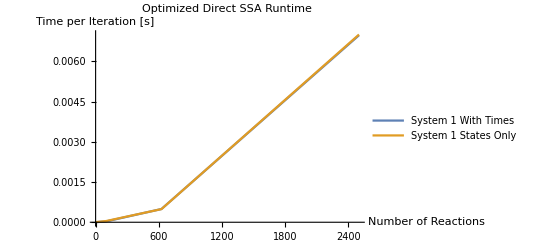

```mathematica
coorsOpt=Flatten[
Table[
Table[{resultsOpt[[i]][[j]][[l]][[3]],resultsOpt[[i]][[j]][[l]][[8]]},{l,Length[resultsOpt[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1]
(*constructionLabels={"System 1","System 2","System 3"};*)
constructionLabels={"System 1"};
statesOnlyLabels={" With Times"," States Only"};
labelsOpt=Flatten[Table[constructionLabels[[i]]<>statesOnlyLabels[[j]],{i,Length[constructionLabels]},{j,Length[statesOnlyLabels]}],1];
ListLinePlot[coorsOpt,PlotLegends->labelsOpt,AxesLabel->{"Number of Reactions","Time per Iteration [s]"},"PlotLabel"->"Optimized Direct SSA Runtime"]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"runtimeResults.mx"},OperatingSystem->$OperatingSystem], resultsOpt];
Export[FileNameJoin[{notebookPath,"runtimeCoors.mx"},OperatingSystem->$OperatingSystem], coorsOpt];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsOpt=Import[FileNameJoin[{notebookPath,"runtimeResults.mx"},OperatingSystem->$OperatingSystem]]
coorsOpt=Import[FileNameJoin[{notebookPath,"runtimeCoors.mx"},OperatingSystem->$OperatingSystem]]
```

{{{{2,2,0.0625,10000,6.25×10^-6},{200,200,0.734375,10000,0.0000734375},{1250,1250,6.6875,10000,0.00066875},{5000,5000,101.234,10000,0.0101234}},{{2,2,0.03125,10000,3.125×10^-6},{200,200,0.46875,10000,0.000046875},{1250,1250,7.15625,10000,0.000715625},{5000,5000,104.281,10000,0.0104281}}},{{{2,2,0.046875,10000,4.6875×10^-6},{200,200,1.34375,10000,0.000134375},{1250,1250,74.5,10000,0.00745},{5000,5000,2089.06,10000,0.208906}},{{2,2,0.09375,10000,9.375×10^-6},{200,200,1.34375,10000,0.000134375},{1250,1250,71.4531,10000,0.00714531},{5000,5000,2097.94,10000,0.209794}}},{{{2,2,0.140625,10000,0.0000140625},{200,200,5.82813,10000,0.000582813},{1250,1250,788.078,10000,0.0788078},{5000,5000,54876.1,10000,5.48761}},{{2,2,1.6875,10000,0.00016875},{200,200,3.92188,10000,0.000392188},{1250,1250,911.25,10000,0.091125},{5000,5000,54126.9,10000,5.41269}}}}

{{{2,6.25×10^-6},{200,0.0000734375},{1250,0.00066875},{5000,0.0101234}},{{2,3.125×10^-6},{200,0.000046875},{1250,0.000715625},{5000,0.0104281}},{{2,4.6875×10^-6},{200,0.000134375},{1250,0.00745},{5000,0.208906}},{{2,9.375×10^-6},{200,0.000134375},{1250,0.00714531},{5000,0.209794}},{{2,0.0000140625},{200,0.000582813},{1250,0.0788078},{5000,5.48761}},{{2,0.00016875},{200,0.000392188},{1250,0.091125},{5000,5.41269}}}